Background

```mathematica
coord ={t,z,φ};

metric =({{-z/(1-z), 0, 0}, {0, 1/(4z(1-z)^2), 0}, {0, 0, 1/(1-z)}});
```

```mathematica
$Assumptions= And[t∈Reals,z>0,z<1,φ>=0,φ<2π];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.Λ ->-(d(d-1))/2/.d->2//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*Exp[ⅈ*J*φ]*ϕ[z]
```

ⅇ^(ⅈ J φ-ⅈ t ω) ϕ[z]

```mathematica
SEstep1 = scalarLaplacian[Φ]-m^2Φ;
SEstep2 = Collect[SEstep1/(Exp[-ⅈ*ω*t]Exp[ⅈ*J*φ]),{ϕ''[z],ϕ'[z],ϕ[z]},Simplify]/.m->0// Simplify
```

((-1+z) ((J^2 z-ω^2) ϕ[z]+4 (-1+z) z (ϕ'[z]+z ϕ''[z])))/z

```mathematica
Solution1=Values[DSolve[SEstep2==0,ϕ[z],z]][[1]][[1]]//FullSimplify
```

(-z)^(-(ⅈ ω)/2) ((-z)^(ⅈ ω) C[2] Hypergeometric2F1[-1/2 ⅈ (J-ω),1/2 ⅈ (J+ω),1+ⅈ ω,z]+C[1] Hypergeometric2F1[1/2 ⅈ (J-ω),-1/2 ⅈ (J+ω),1-ⅈ ω,z])

```mathematica
InftyBehaviour=Normal[Series[Solution1,{z,1,0}]] //FullSimplify
```

ⅇ^(-(π ω)/2) ((ⅇ^(π ω) C[1] Gamma[1-ⅈ ω])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1-1/2 ⅈ (J+ω)])+(C[2] Gamma[1+ⅈ ω])/(Gamma[1-1/2 ⅈ (J-ω)] Gamma[1+1/2 ⅈ (J+ω)]))

```mathematica
Solution2 = Solution1 /.C[2]->-C[1]Exp[π ω]Gamma[1-(ⅈ (J-ω))/2]Gamma[1+(ⅈ (J+ω))/2] Gamma[1-ⅈ ω]/(Gamma[1+(ⅈ (J-ω))/2]Gamma[1-(ⅈ (J+ω))/2] Gamma[1+ⅈ ω])
```

(-z)^(-(ⅈ ω)/2) (-(ⅇ^(π ω) (-z)^(ⅈ ω) C[1] Gamma[1-1/2 ⅈ (J-ω)] Gamma[1-ⅈ ω] Gamma[1+1/2 ⅈ (J+ω)] Hypergeometric2F1[-1/2 ⅈ (J-ω),1/2 ⅈ (J+ω),1+ⅈ ω,z])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1+ⅈ ω] Gamma[1-1/2 ⅈ (J+ω)])+C[1] Hypergeometric2F1[1/2 ⅈ (J-ω),-1/2 ⅈ (J+ω),1-ⅈ ω,z])

```mathematica
InftyBehaviourComprobation=Normal[Series[Solution2,{z,1,0}]] //FullSimplify
```

0

```mathematica
BoundaryBehaviour=Normal[Series[Solution2,{z,0,0}]]//FullSimplify
```

(-z)^(-(ⅈ ω)/2) C[1] (1-(z^(ⅈ ω) Gamma[-1/2 ⅈ (2 ⅈ+J-ω)] Gamma[1-ⅈ ω] Gamma[1/2 ⅈ (-2 ⅈ+J+ω)])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1+ⅈ ω] Gamma[1-1/2 ⅈ (J+ω)]))

```mathematica
Q1=-(Gamma[-1/2 ⅈ (2 ⅈ+J-ω)] Gamma[1-ⅈ ω] Gamma[1/2 ⅈ (-2 ⅈ+J+ω)])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1+ⅈ ω] Gamma[1-1/2 ⅈ (J+ω)])// FullSimplify
```

-(Gamma[-1/2 ⅈ (2 ⅈ+J-ω)] Gamma[1-ⅈ ω] Gamma[1/2 ⅈ (-2 ⅈ+J+ω)])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1+ⅈ ω] Gamma[1-1/2 ⅈ (J+ω)])

```mathematica
P1=1
```

1

One would have to check that Abs[Q1]=1

### Trying to obtain Quantization of Omega

```mathematica
alpha=0;
```

```mathematica
beta=Arg[Q1]//FullSimplify
```

Arg[-(Gamma[-1/2 ⅈ (2 ⅈ+J-ω)] Gamma[1-ⅈ ω] Gamma[1/2 ⅈ (-2 ⅈ+J+ω)])/(Gamma[1+1/2 ⅈ (J-ω)] Gamma[1+ⅈ ω] Gamma[1-1/2 ⅈ (J+ω)])]

Sigma=0

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,	
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.J->i,{ω,0.00015},WorkingPrecision->100]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

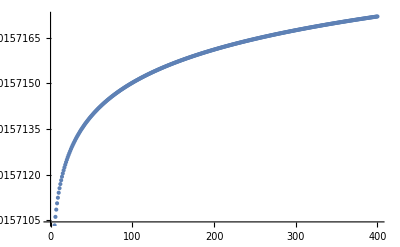

```mathematica
ListPlot[OmegaQuantization]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantization]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantization,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantization];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

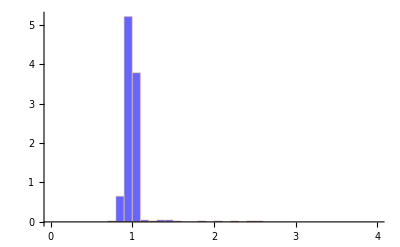

```mathematica
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantization]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

Sigma=2

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=400, i++,
Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,2/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationtwo=Append[OmegaQuantizationtwo,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (-Sin[Arg[-(Gamma[-1/2 ⅈ Plus[«2»]] Gamma[1+Times[«2»]] Gamma[1/2 ⅈ Plus[«2»]])/(Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Plus[«2»]])]]=={-Sin[20002.5 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-(Gamma[-1/2 ⅈ Plus[«2»]] Gamma[1+Times[«2»]] Gamma[1/2 ⅈ Plus[«2»]])/(Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Plus[«2»]])]]=={-Sin[20003.7 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-(Gamma[-1/2 ⅈ Plus[«2»]] Gamma[1+Times[«2»]] Gamma[1/2 ⅈ Plus[«2»]])/(Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Plus[«2»]])]]=={-Sin[19997.6 ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

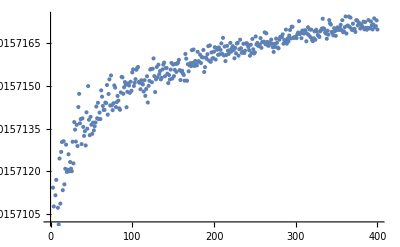

```mathematica
ListPlot[OmegaQuantizationtwo]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationtwo]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationtwo,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationtwo];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

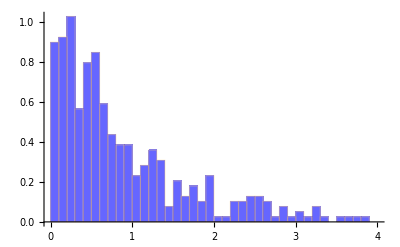

```mathematica
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationtwo]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

Sigma=0.025

```mathematica
OmegaQuantizationthree = {};
For[i=1, i<=400, i++,
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.025/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationthree=Append[OmegaQuantizationthree,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (-Sin[Arg[-(Gamma[-1/2 ⅈ Plus[«2»]] Gamma[1+Times[«2»]] Gamma[1/2 ⅈ Plus[«2»]])/(Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Plus[«2»]])]]=={-Sin[20000.1 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-(Gamma[-1/2 ⅈ Plus[«2»]] Gamma[1+Times[«2»]] Gamma[1/2 ⅈ Plus[«2»]])/(Gamma[Plus[«2»]] Gamma[Plus[«2»]] Gamma[Plus[«2»]])]]=={-Sin[20000. ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

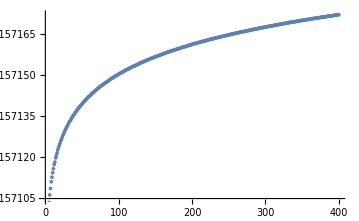

```mathematica
ListPlot[energyLevels]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationthree]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationthree,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationthree];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

```mathematica
histogram=Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}];
```

```mathematica
wignerDyson[x_]:=(32/Pi^2) x^2 Exp[-(4/Pi) x^2];
wdPlot=Plot[wignerDyson[x],{x,0,3},PlotStyle->{Blue,Thick}];
```

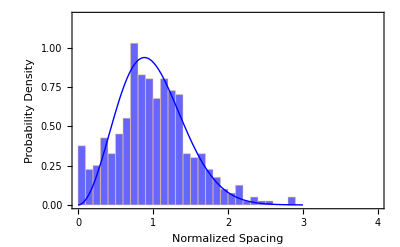

```mathematica
Show[histogram,wdPlot,PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationthree]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```